```mathematica
PacletUpdate["EntityFramework"]
```

## Retrieve models from repositories specified and returning model in Matrix Format (MF)

```mathematica
dir:=NotebookDirectory[];
```

```mathematica
(*After Docker setup, populate your new database with models from the JWS online as well as Biomodels repository*)
cookies = URLFetch["localhost/rest/models","Cookies","StoreCookies"->False];

(*Model Import Functions*)
(*Upload Models from urls to server adress specified JWSOnline*)
impMods[linkName_]:=Block[{},
URLExecute[HTTPRequest["localhost/rest/fetch/?type=sbml&redirect={redirect}&remote="<>ToString[linkName],{"Cookies"->cookies}]]
];

(*Installing Biomodels webservice*)
Needs["WebServices`"]
Quiet[InstallService["https://www.ebi.ac.uk/biomodels-main/services/BioModelsWebServices?wsdl"]];
```

```mathematica
(*URLS for Calls of SBML Models*)
Print["Fetching model urls from BioModels and JWSOnline and relable with url id"];
urlLink=Join["http://www.ebi.ac.uk/biomodels-main/download?mid="<>#&/@getAllCuratedModelsId[],StringReplace[#[[1,2]],"?format=json"->"sbml"]&/@URLExecute["https://jjj.bio.vu.nl/rest/models/?format=json"]];

urls =Which[
StringMatchQ[#,"http://www.ebi.ac.uk/biomodels-main/download?mid="~~__],
StringDelete[#,"http://www.ebi.ac.uk/biomodels-main/download?mid="]->#,
StringMatchQ[#,"https://jjj.bio.vu.nl/rest/models/"~~__~~"/sbml"],
StringDrop[StringDelete[#,"https://jjj.bio.vu.nl/rest/models/"],-5]->#
]&/@urlLink;
```

Fetching model urls from BioModels and JWSOnline and relable with url id

```mathematica
urls
```

```mathematica
(*Import models, from urls above to local Docker JWSonline*)
modelsIn = {};
j = 0;
SetDirectory[dir];
Monitor[Do[j+=1 ;AppendTo[modelsIn,Check[urls[[i,1]]->impMods[urls[[i,2]]],PutAppend[urls[[i,1]]->"Import_Error","Log.txt"],{URLExecute::invhttp}]],{i,1,Length[urls]}],ToString[(j/Length[urls])*100.0]<>" % : "<>urls[[j,1]]];
```

URLExecute::invhttp: Empty reply from server.

```mathematica
(*Removing redundant Brackets and failed models*)
mdIn=DeleteCases[Replace[modelsIn,{x_List}:>x,{0,-3}],x_/;StringMatchQ[ToString[x],__~~"-> {details -> /rest/models/slug/, type -> model, id ->"~~__]==False];
(*Compare initial with final model list*)
Length[modelsIn]
Length[mdIn]
```

1223

```mathematica
(*Retrieve models in matrix format*)
mfMods={};
SetSharedVariable[mfMods];
j=0;
Monitor[Do[j+=1;AppendTo[mfMods,
mdIn[[i,1]]-> URLExecute[HTTPRequest["localhost/rest/models/"<>ToString["slug"/.Flatten[Values[mdIn[[i]]]]]<>"/mf",{"Cookies"->cookies}]]],{i,1,Length[mdIn]}],ToString[(j/Length[urls])*100.0]<>"% : "<>urls[[j,1]]];
```

```mathematica
cleanMods=DeleteCases[mfMods,x_/;Head[x[[2]]]==Failure];
cleanMods//Length
mfMods//Length
```

12

12

```mathematica
mfMods
```

```mathematica
SetDirectory[dir]
PutAppend[#,"mfMods.csv"]&/@cleanMods;
```

/Users/errust/Desktop/Run_1

## Runtime functions

```mathematica
SetDirectory["/Users/jls/Sites/JWSBase/Mathematica/packages/modellingPackages"]
Needs["modelManipulationPackageV2`"];
Needs["MCAPackageV2`"];
Needs["modelPlotPackageV2`"];
Needs["oscillationPackageV2`"];
Print;Unprotect[Print];Print=Null&;

(*Handling Errors in sub kernels*)
(*Keq and flux calculations*)
(*Given a MF model of example modelName->{...model...}, returns the Flux Control Coefficient as well as the disequilibrium ratio*)

getKeqVsFluxCC[mod_]:=Module[{erPos,newModel,slug,pieceCheck,rateStoich,fluxSeperate,fluxCrev, fullN,rates,variables,rateEquations,parameters,initialValues,assignments, stst,steadyStateVariables,prodNum,subNum,prods,subs, rate,revPos1,revPos,revRates,Keq,gamma,rates0,solve,fluxC,gammaSub,gammaKeq,disEq,finOut, fluxCC,out,elaMat,steps,fluxMedian,mElas,outtest,keys, gammaKey, solKey},

Catch[
(*Initialize Slug and Model*)
newModel=mod[[2]];
(*steps=mod[[3]];*)
slug = mod[[1]];

(*Initialize variables from model*)
(*Checking for reduced stoich matrix*)
If[newModel[[7]]≠{{},{},{}},
fullN={Join[newModel[[1,1]],newModel[[7,1]]],Join[newModel[[1,2]],newModel[[7,2]]],DeleteDuplicates[Join[newModel[[1,3]],newModel[[7,3]]]]},fullN = newModel[[1]]];
rateStoich = Transpose[fullN[[2]]];
rates = fullN[[3]];
variables = fullN[[1]];
rateEquations = newModel[[2]];
parameters = newModel[[4]];
initialValues = newModel[[3]];
assignments = newModel[[5]];

(*create assignment rules indicating products and substrates spesific to the rate equation*)
prods=GroupBy[Sort[fullN[[3,#[[2]]]]-> fullN[[1,#[[1]]]]&/@Position[fullN[[2]],x_/;x>0]],First->Last];
subs=GroupBy[Sort[fullN[[3,#[[2]]]]-> fullN[[1,#[[1]]]]&/@Position[fullN[[2]],x_/;x<0]],First->Last];

(*Test whether rate equation contains a negative parts in the numerator. Select theses reactions as reversible. Discarding all irriversable reactions as no disequilibrium ratio can be determined*)

revPos1 = {};
check={};
Do[
rate = rateEquations[[i,2]];
Do[If[(Position[Numerator[rate[[j]]],-1,Infinity]//Length)≠0,AppendTo[revPos1,i]],
{j,1,Length[rate]}]
AppendTo[check,rate];
,{i,1,Length[rateEquations]}];

revPos1=DeleteDuplicates[revPos1];

If[Length[revPos1]≠0,

PutAppend[slug->"Has_Rev_Rates","Log.txt"];
(*Flux Control Calculations*)
fluxC = FluxSumTest[slug,newModel(*,steps*)];

erPos = Position[fluxC//Values,"Flux Summation Error"];

(*Remove flux errors from revPos*)
revPos=removeFrom2[revPos1,Flatten[erPos]];

(*Test For negative flux coeficients and tag models for further investigation*)
If[AnyTrue[fluxC[[revPos]],Negative],PutAppend[slug-> "Negative_FCC","Log.txt"]];

fluxMedian=Thread[Keys[prods]-> Median[Select[Keys[prods]/.fluxC,Head[#]==Real&]]];
revRates = rates[[revPos]];

elaMat=elasMat[newModel,1500];
mElas=Max[Flatten[elaMat[[2]],1]];
If[mElas>1*10^-10,

(*Find steadystate solutions using the MCAPackageV2*)
stst = Quiet[Check[ststSolMatFormR[newModel,1500,{},{MaxIterations-> 1000},"True"],PutAppend[slug->"StadyState_Error","Log.txt"],{Power::infy,ReplaceAll::reps}]];

steadyStateVariables = Join[stst[[1]],stst[[3]]];
(*Assumptions on iterations*)

gamma = Thread[fullN[[3]]->(Times@@Thread[Check[fullN[[1]]^#,Return[0],{Power::infy}]]&/@Transpose[fullN[[2]]])];

(*Create product over substrate symbolic equations. Assumption is made on the reaction order of mass action based on the stoichiometry*)

keys=Keys[prods];
(*Define rate equations at equilibrium*)

(*Keq and disequilibrium calculations:
Solving the rate equations in terms of specified products and substituting result into gamma to obtain Keq value according to the haldane princeple
Assumption is made: The Keq value calculated from the mathematical model is not an indication of the true Keq. However since the control calculations are also determined by the same set of mathematical equations, it is safe to assume that the comparitive error order between the Keq and flux calculations would be consistent and therefore would still be reflective of biological relationships*)

(*Main Calculations*)
If[AllTrue[steadyStateVariables,Head[#]==Rule&],
Do[If[False==AnyTrue[Join[keys[[i]]/.prods,keys[[i]]/.subs],FreeQ[Numerator[keys[[i]]/.rateEquations],#]&],
(*Formatting data for export*)
gammaKey = keys[[i]]//.gamma;
solKey = Flatten[Solve[(keys[[i]]//.rateEquations)==0,First[keys[[i]]/.prods]]];
disEq=Check[gammaKey/(gammaKey/.solKey)/.assignments/.parameters/.steadyStateVariables,PutAppend[slug-> keys[[i]],keys[[i]]-> "Devision_by_Zero","Log.txt"],{Power::infy}];
PutAppend[{"modName"-> slug,"Reaction"->keys[[i]],"DisEq"->disEq,"FluxCC"->keys[[i]]/.fluxC,"FluxCCMed"->keys[[i]]/.fluxMedian},"finalCal_Thesis.txt"];
PutAppend[slug->"Passed","Log.txt"];
,
PutAppend[slug->keys[[i]],keys[[i]]-> "No_Product_or_Substrate","Log.txt"]
];
,{i,1,Length[prods]}];
,PutAppend[slug->"Replacement_Errors","Log.txt"]
];
,PutAppend[slug->"Small_ElastMax","Log.txt"]];
,PutAppend[slug->"No_Reversible_Reactions","Log.txt"]];
];
];

(*Model Checking/Filtering Functions*)
(*ListCompare Function to exclude Flux Summation Errors within reversible rates*)
removeFrom2[b_List,a_List]:=Module[{f,g},(f[#]=-#2)&@@@Tally[a];
g[x_]/;f[x]<0:=f[x]++;
g[_]=True;
Select[b,g]]

(*Flux Summation Test*)
FluxSumTest[slug_String,model_(*,steps_*)] :=Module[{fluxMat,(*fluxSums,*)fluxDiag},
fluxMat = Check[fullFluxMatPseudo[model,1500],PutAppend[slug-> "Flux_Calculation_Error","Log.txt"],{Return::nofunc}];
If[ToString[fluxMat[[1]]]== "ERROR in steady state computation for calculating fullCmat:",PutAppend[slug-> "Steady_State_Errors","Log.txt"];,
fluxDiag = Thread[fluxMat[[1]]->Diagonal[fluxMat[[2]]]];
(*Flux Summation Test*)
fluxSums ={};Do[ If[Round[Total[#],0.1]==1.,AppendTo[fluxSums,fluxDiag[[i]]],PutAppend[slug-> fluxDiag[[i,1]],fluxDiag[[i,1]]->"Flux_Sumation_Error","Log.txt"]]&[fluxMat[[2]][[i]]],{i,1,Length[fluxDiag]}];
If[fluxSums=={},PutAppend[slug-> "No_Flux_Returns","Log.txt"],Return[fluxSums]];
];
];

mcaOptimize[func_Symbol,mod_,initStep_,Longest[funcAtribs___]]:=Module[{step},Check[Check[{step=initStep,func[mod,Sequence@@({funcAtribs}/.step)]}
,step={"preInt"->Values[initStep][[1]]*10,"iterSize"-> Values[initStep][[2]]};
mcaOptimize[func,mod,step,funcAtribs]
,FindRoot::lstol],
step={"preInt"->Values[initStep][[1]]*10,"iterSize"-> Values[initStep][[2]]*10};
mcaOptimize[func,mod,step,funcAtribs]
,FindRoot::cvmit]
]

(*Testing to see wether model has oscilatory properties, finding optimized preIntegration and iterator count*)
OscilationTest[mod_]:=Module[{initStep,eigenUnit,stateTest,newMod,jacCal},
(*initStep={"preInt"->1000,"iterSize"->100};*)
jacCal=jacobianMatrix[mod];
eigenUnit = ReIm[Eigenvalues[jacCal[[2]]]];
stateTest[eigenUnit_]:=(Positive[eigenUnit[[1]]]||Positive[eigenUnit[[1]]]&&eigenUnit[[2]]≠0);
AnyTrue[eigenUnit,stateTest]
];

(*Checking for Piecewise functions that may cause errors*)
CheckPiecewise[expr_]:=StringFreeQ[ToString[expr],"Piecewise"];

(*Checking for Imaginary parts within each expression. We are working within the real numbers*)
ImaginaryQ[expr_]:=!FreeQ[expr,_Complex];

(*Main model check wrapper*)
chkMods[modin_]:=Module[{mod,os},

SetDirectory["/Users/jls/Sites/JWSBase/Mathematica/packages/modellingPackages"];
Needs["modelManipulationPackageV2`"];
Needs["MCAPackageV2`"];
Needs["modelPlotPackageV2`"];
Needs["oscillationPackageV2`"];
Print;Unprotect[Print];Print=Null&;

SetDirectory["/Users/errust/Desktop/Run_1"];

Catch[
PutAppend["All_Models"->modin[[1]],"Log.txt"];
mod=modin[[2]];
Which[
mod[[1]]=={{},{},{}},
PutAppend[modin[[1]]->"No_Stoichiometries","Log.txt"],
mod[[8]]≠ {},PutAppend[modin[[1]]->"Events","Log.txt"],
CheckPiecewise[mod]==False,PutAppend[modin[[1]]->"Piecewise","Log.txt"],
OscilationTest[mod]==True,PutAppend[modin[[1]]-> "Oscilatory","Log.txt"],
1==1,getKeqVsFluxCC[modin[[1]]->  Check[switchMoietiesToMoietyRules[modin[[2]]],PutAppend[modin[[1]]->"Devision_by_Zero","Log.txt"],{Power::infy}]]];
]
];
```

/Users/jls/Sites/JWSBase/Mathematica/packages/modellingPackages

## Load Models from exported file

```mathematica
SetDirectory[dir]
cleanMods=ReadList["mfMods.csv"];
Length[cleanMods]
```

/Users/errust/Desktop/Run_1

778

## Porting models through runtime code and directing to output based on criteria defined in thesis

```mathematica
(*Main Wrapper*)
SetSharedVariable[j,cleanMods];
j=1;
Monitor[ParallelDo[
Quiet[TimeConstrained[Catch[chkMods[cleanMods[[i]]]],1500,PutAppend[cleanMods[[i,1]]-> "Timed_Out","Log.txt"]]];
j+=1;
,{i,1,Length[cleanMods]},Method->"CoarsestGrained"],cleanMods[[j,1]]<>" : "<>ToString[j]]
```

```mathematica
GroupBy[Values[cleanDat],First][[1,All]]
```

{{branch3,model`v 1,0.21525,0.688982,0.655509},{branch3,model`v 2,0.,0.655509,0.655509},{branch3,model`v 3,0.,0.655509,0.655509}}

0.21525

## Data Analysis

```mathematica
"No_Reversible_Reactions"
```

## Log and Data Visualisation

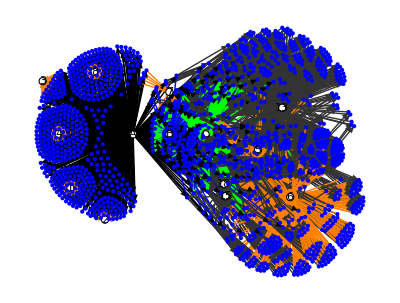

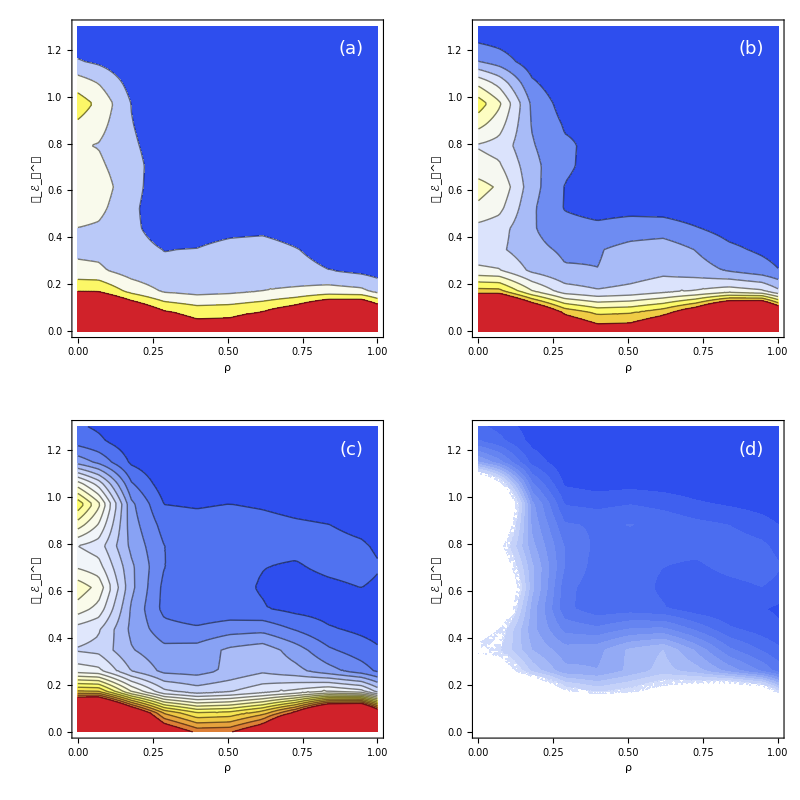

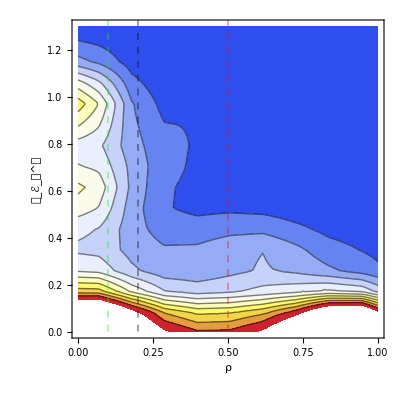

```mathematica
log=Replace[ReadList["/Users/errust/Desktop/Run_1/Log.txt"],{"All_Models"->"A","Has_Rev_Rates"->"B","Passed"-> "C", "No_Stoichiometries"->"1","Events"->"2","Piecewise"->"3","Oscilatory"->"4","Devision_by_Zero"->"5","Flux_Sumation_Error"->"6","Timed_Out"->"7","No_Reversible_Reactions"->"8", "Import_Error"->"9", "Negative_FCC"->"10","StadyState_Error"->"11", "Devision_by_Zero"->"12","No_Product_or_Substrate"->"13","Replacement_Errors"->"14","Small_ElastMax"->"15","No_Reversible_Reactions"->"16","Flux_Calculation_Error"->"17","No_Flux_Returns"->"18"},2];

(*List of labels to create*)
lblLst={"A","B","C","1","2", "3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18"};

(*Specifying edge directives for coloring log Visualisation*)
drawEdge[ends_,fromTo_,label_]:=Join[edgeStyle[fromTo],{Arrowheads[{0.002}],Arrow[ends]}];

edgeStyle[{"A",___}]:={Black,Thin};
edgeStyle[{___,"C"}]:={Green,Thin};
edgeStyle[{___,"B"}]:={Blue,Thin};
edgeStyle[{___,"1"}|{___,"2"}|{___,"3"}|{___,"4"}|{___,"5"}|{___,"6"}|{___,"7"}|{___,"8"}]:={Orange,Thin};
edgeStyle[_]:={GrayLevel[0.2],Thin};

(*Plotting Graph of Log*)
graph = GraphPlot[log,EdgeRenderingFunction->drawEdge, VertexRenderingFunction->(If[MemberQ[lblLst,#2],{White,EdgeForm[Black],Disk[#,5],Black,Text[#2,#1]},{Blue,Point[#1],PointSize[Tiny]}]&),VertexLabeling->Tooltip,VertexCoordinateRules->{"A"->{-50,0},"B"->{0,0},"C"->{50,0}}];

(*Waiting for graph to load*)
Pause[1]

(*Reading, cleaning, and inverting data around equilibrium (Disequilibrium ratio of 1) in order to visualise*)
Quiet[
finCal =ReadList["/Users/errust/Desktop/Run_1/finalCal_Thesis.txt"];
invert={#[[1]],#[[2]],If[#[[3,2]]>1,#[[3,1]]->1/#[[3,2]],#[[3]]],#[[4]],#[[5]]}&/@finCal;
cleanDat=DeleteCases[Cases[invert,{_String->_String,_String->_Symbol,_String->_Real,_String->_Real,_String->_Real}],x_/;"DisEq"/.x==0|"DisEq"/.x==1];
median:=Median[#[[All,3,2]]]&/@GroupBy[Values[cleanDat],First];
medDat=Insert[#,#[[1]]/.median,6]&/@Values[cleanDat];
vals = cleanDat[[All,3;;4]]//Values;
ker = SmoothKernelDistribution[vals];
];

parabola=Fit[vals,{1,x},x];

(*Constructing Probability Density Function of data*)
pdf= PDF[ker,{x,y}];

(*Creating Grids*)
Show[graph,ImageSize->Full]

grid=GraphicsGrid[{{ContourPlot[pdf,{x,0,1},{y,0,1.3},ColorFunction->"TemperatureMap",Contours->4,ClippingStyle->Automatic,Epilog->Inset[Style["(a)",18,White],Offset[{-20,-20},Scaled[{1,1}]],{Right,Top}],Frame->True,FrameLabel->{"ρ","𝒞_ℰ_𝒾^𝒥"},AspectRatio->1,ImagePadding->{{60,10},{50,10}}],
ContourPlot[pdf,{x,0,1},{y,0,1.3},ColorFunction->"TemperatureMap",Contours->8,ClippingStyle->Automatic,Epilog->Inset[Style["(b)",18,White],Offset[{-20,-20},Scaled[{1,1}]],{Right,Top}],Frame->True,FrameLabel->{"ρ","𝒞_ℰ_𝒾^𝒥"},AspectRatio->1,ImagePadding->{{60,10},{50,10}}]},{ContourPlot[pdf,{x,0,1},{y,0,1.3},ColorFunction->"TemperatureMap",Contours->16,ClippingStyle->Automatic,Epilog->Inset[Style["(c)",18,White],Offset[{-20,-20},Scaled[{1,1}]],{Right,Top}],Frame->True,FrameLabel->{"ρ","𝒞_ℰ_𝒾^𝒥"},AspectRatio->1,ImagePadding->{{60,10},{50,10}}],
ContourPlot[pdf,{x,0,1},{y,0,1.3},ColorFunction->"TemperatureMap",Contours->32,ClippingStyle->Automatic,Epilog->Inset[Style["(d)",18,White],Offset[{-20,-20},Scaled[{1,1}]],{Right,Top}],Frame->True,FrameLabel->{"ρ","𝒞_ℰ_𝒾^𝒥"},AspectRatio->1,ImagePadding->{{60,10},{50,10}}]}},Spacings->{1,1},AspectRatio->1,Frame->All,ImageSize->Full]

ContourPlot[pdf,{x,0,1},{y,0,1.3},GridLines->{{{0.5,Red},{0.1,Green},{0.2,Black}},None},GridLinesStyle->Directive[Red, Dashed,Thick],Contours->10,ColorFunction->"TemperatureMap",FrameLabel->{"ρ","𝒞_ℰ_𝒾^𝒥"},ImageSize->Full]
```

```mathematica
assmus = "assmus"->{{{model`ADPGam[t],model`ADPam[t],model`ADPcyt[t],model`ATPam[t],model`ATPcyt[t],model`DHAPcyt[t],model`F16BPcyt[t],model`F6Pcyt[t],model`Fructose[t],model`G1Pam[t],model`G1Pcyt[t],model`G6Pam[t],model`G6Pcyt[t],model`GAPcyt[t],model`Glucoseam[t],model`Glucosecyt[t],model`PEPcyt[t],model`PGA2cyt[t],model`PGA3am[t],model`PGA3cyt[t],model`PPam[t],model`PPcyt[t],model`Pam[t],model`Pcyt[t],model`Sucrose[t],model`UDPGcyt[t],model`UDPcyt[t],model`UTPcyt[t]},{{0,0,0,0,0,0,0,0,0,1.0,0,0,-1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1.0,0,1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-17.0,1.0,0,0,-1.0,1.0,0,0,0,1.0,0,0,0,0,0,0,0,0,1.0,0,0,0,0,1.0,0,0,1.0,0,0},{0,0,0,0,0,0,0,0,0,-1.0,1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,17.0,-1.0,0,0,1.0,-1.0,0,0,0,-1.0,0,0,0,0,0,0,0,0,-1.0,0,0,0,0,-1.0,0,0,-1.0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.0,-1.0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.0,1.0,-1.0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.0,0,0,0,1.0,-1.0,-1.0,-1.0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1.0,0,0,0,0,0,0,0,0,0,0,-1.0,0,-1.0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1.0,0,0,0,1.0,0,-1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.0,0,-1.0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.0,0,-1.0,-1.0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.0,1.0,1.0,-1.0,1.0,0,0,0,0,0,0,0,0},{0,-6.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.0,1.0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.0,0,-1.0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1.0,0,0,0,0,1.0,0,0,-1.0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1.0,-1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1.0,-1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.0,0,0,0,0,0,0,0,0,0,0,0},{0,6.0,0,-1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1.0,1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.0,0,0,-1.0,0,0,0},{0,0,0,0,0,0,0,-1.0,2.0,0,0,0,0,-1.0,0,0,0,1.0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-17.0,1.0,0,0,0,0,1.0,0,0,0,0,0,0,0,0,0,-1.0,0,0,0,0,0,0,0,1.0,1.0,0,0,0},{1.0,0,0,0,0,0,0,0,0,0,0,-1.0,0,0,0,0,0,0,0,0,0,0,1.0,0,0,1.0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.0,1.0,0,-1.0,0,0,0,0},{0,0,0,0,0,0,-1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.0,0,0,1.0,0,0,0,0},{0,0,0,0,0,0,1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.0,0,0,0,0,0,0}},{model`v 1,model`v 10,model`v 11,model`v 12,model`v 13,model`v 14,model`v 15,model`v 16,model`v 17,model`v 18,model`v 19,model`v 2,model`v 20,model`v 21,model`v 22,model`v 23,model`v 24,model`v 25,model`v 26,model`v 27,model`v 28,model`v 29,model`v 3,model`v 30,model`v 4,model`v 5,model`v 6,model`v 7,model`v 8,model`v 9}},{model`v 1->model`VSucUpt*(model`kforwardSucUpt*model`xsucrose-model`kbackwardSucUpt*model`Sucrose[t]),model`v 10->(model`VmaxGAPDH*(1-(model`ATPcyt[t]*model`PGA3cyt[t])/(model`KeqGAPDH*model`ADPcyt[t]*model`GAPcyt[t]*model`Pcyt[t])))/6,model`v 11->(model`kATPcons*model`VATPcons*model`ATPcyt[t])/model`ADPcyt[t],model`v 12->(model`VmaxPGlyM*(-(model`PGA2cyt[t]/model`KeqPGlyM)+model`PGA3cyt[t]))/(model`KmPGA3PGlyM+(model`KmPGA3PGlyM*model`PGA2cyt[t])/model`KmPGA2PGlyM+model`PGA3cyt[t]),model`v 13->(model`Vmaxeno*(-(model`PEPcyt[t]/model`Keqeno)+model`PGA2cyt[t]))/(model`KmPGA2eno+(model`KmPGA2eno*model`PEPcyt[t])/model`KmPEPeno+model`PGA2cyt[t]),model`v 14->(model`VmaxPK*model`ADPcyt[t]*model`PEPcyt[t])/(model`KmADPPK*model`KmPEPPK*(1+model`ATPcyt[t]/model`KmATPPK+(model`xpyruvate*model`ATPcyt[t])/(model`KmATPPK*model`KmpyruvatePK)+model`PEPcyt[t]/model`KmPEPPK+(model`ADPcyt[t]*model`PEPcyt[t])/(model`KmADPPK*model`KmPEPPK))),model`v 15->model`VNDPK*(model`kforwardNDPK*model`ATPcyt[t]*model`UDPcyt[t]-model`kbackwardNDPK*model`ADPcyt[t]*model`UTPcyt[t]),model`v 16->model`VPexp*(model`kforwardPexp*model`Pam[t]-model`kbackwardPexp*model`Pcyt[t]),model`v 17->model`VmaxpPPase*(1-model`Pam[t]^2/(model`KeqpPPase*model`PPam[t])),model`v 18->(model`VmaxAGPase*(1+model`PGA3am[t]/model`KaPGA3AGPase)*(model`ATPam[t]*model`G1Pam[t]-model`ADPGam[t]*model`PPam[t]))/((model`KmATPAGPase*(1+model`ADPGam[t]/model`KmADPGAGPase)+model`ATPam[t])*(1+model`Pam[t]/model`KiPAGPase)*(model`G1Pam[t]+model`KmG1PAGPase*(1+model`PPam[t]/model`KmPPAGPase))),model`v 19->model`VAT*(-(model`kbackwardAT*model`ADPcyt[t]*model`ATPam[t])+model`kforwardAT*model`ADPam[t]*model`ATPcyt[t]),model`v 2->(model`Vmaxinv*model`Sucrose[t])/(model`KmSucroseinv*(1+model`Glucosecyt[t]/model`KiGlucoseinv)*(1+model`Fructose[t]/model`KiFructoseinv+model`Sucrose[t]/model`KmSucroseinv)),model`v 20->(model`VmaxStSynth*model`ADPGam[t])/(model`KmADPGStSynth+model`ADPGam[t]),model`v 21->(model`VforwardStPase*(-(model`G1Pam[t]/model`KeqStPase)+model`Pam[t]))/(model`KmPStPase+(model`KmPStPase*model`G1Pam[t])/model`KmG1PStPase+model`Pam[t]),model`v 22->model`Vmaxdegr/(1+model`Glucoseam[t]/model`KiGlucosedegr),model`v 23->model`VmaxpPGM*(1-model`G6Pam[t]/(model`KeqpPGM*model`G1Pam[t])),model`v 24->model`VGexp*(model`kforwardGexp*model`Glucoseam[t]-model`kbackwardGexp*model`Glucosecyt[t]),model`v 25->model`VG6Pexp*(-(model`kbackwardG6Pexp*model`G6Pcyt[t]*model`Pam[t])+model`kforwardG6Pexp*model`G6Pam[t]*model`Pcyt[t]),model`v 26->model`VPGA3imp*(-(model`kbackwardPGA3imp*model`G6Pcyt[t]*model`PGA3am[t])+model`kforwardPGA3imp*model`G6Pam[t]*model`PGA3cyt[t]),model`v 27->(model`VmaxGK*model`ATPcyt[t]*model`Glucosecyt[t])/(2*model`KmATPHK1*model`KmGlucoseHK1*(1+model`ADPcyt[t]/model`KiADPHK1+model`ATPcyt[t]/model`KmATPHK1)*(1+model`G6Pcyt[t]/model`KiG6PHK1)*(1+model`Fructose[t]/model`KmFructoseHK1+model`Glucosecyt[t]/model`KmGlucoseHK1))+(model`VmaxGK*model`ATPcyt[t]*model`Glucosecyt[t])/(2*model`KmATPHK2*model`KmGlucoseHK2*(1+model`ADPcyt[t]/model`KiADPHK2+model`ATPcyt[t]/model`KmATPHK2)*(1+model`Fructose[t]/model`KmFructoseHK2+model`Glucosecyt[t]/model`KmGlucoseHK2)),model`v 28->(model`VmaxPGI*(-(model`F6Pcyt[t]/model`KeqPGI)+model`G6Pcyt[t]))/(model`KmG6PPGI+(model`KmG6PPGI*model`F16BPcyt[t])/model`KiF16BPPGI+(model`KmG6PPGI*model`F6Pcyt[t])/model`KmF6PPGI+model`G6Pcyt[t]+(model`KmG6PPGI*model`PEPcyt[t])/model`KiPEPPGI),model`v 29->model`VmaxcPGM*(1-model`G6Pcyt[t]/(model`KeqcPGM*model`G1Pcyt[t])),model`v 3->(model`VmaxSSynth*model`Fructose[t]*(1-(model`Sucrose[t]*model`UDPcyt[t])/(model`KeqSSynth*model`Fructose[t]*model`UDPGcyt[t]))*model`UDPGcyt[t])/(model`KmSSynthFructose*model`KmSSynthUDPG*(1+model`Glucosecyt[t]/model`KiSSynthGlucose)*(1+(model`Sucrose[t]*model`UDPcyt[t])/(model`KmSSynthSucrose*model`KmSSynthUDP)+(model`Fructose[t]*model`UDPGcyt[t])/(model`KmSSynthFructose*model`KmSSynthUDPG))),model`v 30->(model`VforwardUGPase*(-((model`PPcyt[t]*model`UDPGcyt[t])/model`KeqUGPase)+model`G1Pcyt[t]*model`UTPcyt[t]))/((model`G1Pcyt[t]+model`KmG1PUGPase*(1+model`PPcyt[t]/model`KmPPUGPase))*(model`KmUTPUGPase*(1+model`UDPGcyt[t]/model`KmUDPGUGPase)+model`UTPcyt[t])),model`v 4->(model`VmaxFK*model`ATPcyt[t]*model`Fructose[t])/(model`KmATPFK*model`KmFructoseFK*(1+model`F6Pcyt[t]/model`KmF6PFK)*(1+model`Fructose[t]/model`KiFructoseFK)*(1+model`ADPcyt[t]/model`KmADPFK+model`ATPcyt[t]/model`KmATPFK+model`Fructose[t]/model`KiFructoseFK)*(1+model`Fructose[t]/model`KmFructoseFK)),model`v 5->(model`VappSPSSPP*(-((model`Pcyt[t]*model`UDPcyt[t])/model`KeqSPSSPP)+model`F6Pcyt[t]*model`UDPGcyt[t]))/(model`KmF6PSPSSPP*model`KmUDPGSPSSPP+(model`KmF6PSPSSPP*model`KmUDPGSPSSPP*model`Sucrose[t])/model`KiSucroseSPSSPP+(model`VratioSPSSPP*model`Pcyt[t]*model`UDPcyt[t])/model`KeqSPSSPP+model`F6Pcyt[t]*model`UDPGcyt[t]),model`v 6->(model`VmaxPFP*(-((model`F16BPcyt[t]*model`Pcyt[t])/model`KeqPFP)+model`F6Pcyt[t]*model`PPcyt[t]))/(model`KmF6PPFP*model`KmPPPFP*(1+model`F16BPcyt[t]/model`KmF16BPPFP+model`F6Pcyt[t]/model`KmF6PPFP+model`Pcyt[t]/model`KmPPFP+model`PPcyt[t]/model`KmPPPFP)),model`v 7->(model`VmaxPFK*model`F6Pcyt[t]*(1+model`F6Pcyt[t]/model`KmF6PPFK)^(-1+model`nPFK))/(model`KmF6PPFK*((1+model`F6Pcyt[t]/model`KmF6PPFK)^model`nPFK+model`LPFK*(1+model`PEPcyt[t]/model`KiPEPPFK)^model`nPFK)),model`v 8->(model`Vmaxald*model`F16BPcyt[t]*(1-(model`DHAPcyt[t]*model`GAPcyt[t])/(model`Keqald*model`F16BPcyt[t])))/(model`KmF16BPald*(1+model`DHAPcyt[t]/model`KmDHAPald+model`F16BPcyt[t]/model`KmF16BPald+model`GAPcyt[t]/model`KmGAPald+(model`DHAPcyt[t]*model`GAPcyt[t])/(model`KmDHAPald*model`KmGAPald)+(model`F16BPcyt[t]*model`GAPcyt[t])/(model`KiGAPald*model`KmF16BPald))),model`v 9->(model`VmaxTPI*(model`DHAPcyt[t]-model`GAPcyt[t]/model`KeqTPI))/(model`KmDHAPTPI+model`DHAPcyt[t]+model`GAPcyt[t])},{model`ADPGam[0]==100.0,model`ADPam[0]==100.0,model`ADPcyt[0]==180.0,model`ATPam[0]==150.0,model`ATPcyt[0]==200.0,model`DHAPcyt[0]==5.0,model`F16BPcyt[0]==1.0,model`F6Pcyt[0]==160.0,model`Fructose[0]==20.0,model`G1Pam[0]==30.0,model`G1Pcyt[0]==30.0,model`G6Pam[0]==550.0,model`G6Pcyt[0]==500.0,model`GAPcyt[0]==1.0,model`Glucoseam[0]==3000.0,model`Glucosecyt[0]==150.0,model`PEPcyt[0]==10.0,model`PGA2cyt[0]==20.0,model`PGA3am[0]==160.0,model`PGA3cyt[0]==150.0,model`PPam[0]==5.0,model`PPcyt[0]==1.0,model`Pam[0]==2000.0,model`Pcyt[0]==2000.0,model`Sucrose[0]==88000.0,model`UDPGcyt[0]==870.0,model`UDPcyt[0]==10.0,model`UTPcyt[0]==20.0},{model`KaPGA3AGPase->10.0,model`KeqGAPDH->1.724,model`KeqPFP->3.3,model`KeqPGI->0.25,model`KeqPGlyM->0.16,model`KeqSPSSPP->7770.0,model`KeqSSynth->2.4,model`KeqStPase->0.18,model`KeqTPI->0.0455,model`KeqUGPase->0.15,model`Keqald->81.0,model`KeqcPGM->17.0,model`Keqeno->6.3,model`KeqpPGM->17.0,model`KeqpPPase->750000.0,model`KiADPHK1->20.0,model`KiADPHK2->100.0,model`KiF16BPPGI->7500.0,model`KiFructoseFK->5000.0,model`KiFructoseinv->180.0,model`KiG6PHK1->4100.0,model`KiGAPald->1000.0,model`KiGlucosedegr->100.0,model`KiGlucoseinv->1000.0,model`KiPAGPase->160.0,model`KiPEPPFK->18.0,model`KiPEPPGI->1100.0,model`KiPSPP->4000.0,model`KiSSynthGlucose->12000.0,model`KiSucroseSPSSPP->5000.0,model`KiUDPSPS->1000.0,model`KmADPFK->13.0,model`KmADPGAGPase->280.0,model`KmADPGStSynth->150.0,model`KmADPPK->20.0,model`KmATPAGPase->180.0,model`KmATPFK->35.0,model`KmATPHK1->80.0,model`KmATPHK2->280.0,model`KmATPPK->86.0,model`KmDHAPTPI->880.0,model`KmDHAPald->100.0,model`KmF16BPPFP->10.0,model`KmF16BPald->6.0,model`KmF6PFK->1300.0,model`KmF6PPFK->290.0,model`KmF6PPFP->500.0,model`KmF6PPGI->150.0,model`KmF6PSPS->5000.0,model`KmF6PSPSSPP->900.0,model`KmFructoseFK->90.0,model`KmFructoseHK1->11000.0,model`KmFructoseHK2->22000.0,model`KmG1PAGPase->100.0,model`KmG1PStPase->2600.0,model`KmG1PUGPase->80.0,model`KmG6PPGI->270.0,model`KmGAPTPI->440.0,model`KmGAPald->100.0,model`KmGlucoseHK1->41.0,model`KmGlucoseHK2->130.0,model`KmPEPPK->20.0,model`KmPEPeno->150.0,model`KmPGA2PGlyM->60.0,model`KmPGA2eno->150.0,model`KmPGA3PGlyM->330.0,model`KmPPAGPase->260.0,model`KmPPFP->10.0,model`KmPPPFP->25.0,model`KmPPUGPase->130.0,model`KmPStPase->6200.0,model`KmSSynthFructose->5900.0,model`KmSSynthSucrose->55000.0,model`KmSSynthUDP->140.0,model`KmSSynthUDPG->1650.0,model`KmSucroseinv->28000.0,model`KmUDPGSPS->3000.0,model`KmUDPGSPSSPP->2000.0,model`KmUDPGUGPase->140.0,model`KmUTPUGPase->120.0,model`KmpyruvatePK->1000.0,model`LPFK->1.0,model`VAT->1.0,model`VATPcons->1.0,model`VG6Pexp->1.0,model`VGexp->1.0,model`VNDPK->1.0,model`VPGA3imp->1.0,model`VPexp->1.0,model`VSucUpt->1.0,model`VappSPSSPP->797.0,model`VforwardStPase->200.0,model`VforwardUGPase->8100.0,model`VmaxAGPase->312.0,model`VmaxFK->376.0,model`VmaxGAPDH->301.0,model`VmaxGK->160.0,model`VmaxHK1->80.0,model`VmaxHK2->80.0,model`VmaxPFK->135.0,model`VmaxPFP->1266.0,model`VmaxPGI->1086.0,model`VmaxPGlyM->541.0,model`VmaxPK->127.0,model`VmaxSPS->1000.0,model`VmaxSSynth->100.0,model`VmaxStSynth->171.0,model`VmaxTPI->4438.0,model`Vmaxald->430.0,model`VmaxcPGM->1842.0,model`Vmaxdegr->114.0,model`Vmaxeno->448.0,model`Vmaxinv->33.0,model`VmaxpPGM->1542.0,model`VmaxpPPase->500.0,model`VratioSPSSPP->1000.0,model`kATPcons->3.0,model`kbackwardAT->0.002,model`kbackwardG6Pexp->0.01,model`kbackwardGexp->0.001,model`kbackwardNDPK->0.001,model`kbackwardPGA3imp->0.01,model`kbackwardPexp->0.1,model`kbackwardSucUpt->0.01,model`kforwardAT->0.002,model`kforwardG6Pexp->0.01,model`kforwardGexp->0.001,model`kforwardNDPK->0.001,model`kforwardPGA3imp->0.01,model`kforwardPexp->0.3,model`kforwardSucUpt->0.01,model`nPFK->2.0,model`xpyruvate->10.0,model`xstarch->1000000.0,model`xsucrose->90000.0,model`default compartment->1.0},{},t,{{model`xpyruvate,model`xstarch,model`xsucrose},{{0,0,0,0,0,1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1.0,-1.0,-1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{model`v 1,model`v 10,model`v 11,model`v 12,model`v 13,model`v 14,model`v 15,model`v 16,model`v 17,model`v 18,model`v 19,model`v 2,model`v 20,model`v 21,model`v 22,model`v 23,model`v 24,model`v 25,model`v 26,model`v 27,model`v 28,model`v 29,model`v 3,model`v 30,model`v 4,model`v 5,model`v 6,model`v 7,model`v 8,model`v 9}},{},{},{},{"time = min","metabolite = umol/L","extent = nmol/gDW"},{"xlog"->"False","ylog"->"False","xrange"->{},"yrange"->{}},{"taskID"->""}};
```

```mathematica
chkMods[assmus]
```

Part::partw: Part {1,2,4,5,7,8,9,10,11,14,16,17,18,19,20,21,22,23,24,26,27,28,29,30} of {model`v 1→0.00689831,model`v 10→0.0000131589,model`v 11→0.650035,model`v 12→0.0053057,model`v 13→0.0155726,model`v 14→0.193931,model`v 15→0.0479288,model`v 16→-0.0679582,model`v 17→0.000294217,model`v 18→0.177937,«10»,model`v 29→0.000146767,model`v 3→0.286846,model`v 30→0.000436016,model`v 4→0.0174409,model`v 5→0.775423,model`v 6→0.869404,model`v 7→0.101084,model`v 8→-0.000564045,model`v 9→0.0000857758} does not exist.

```mathematica
rateEquations=assmus[[2,2]];
```

```mathematica
revPos1 = DeleteDuplicates[revPos1]
```

{1,2,4,5,7,8,9,10,11,14,16,17,18,19,21,22,23,24,26,27,28,29,30}

```mathematica
rateEquations[[20]]
```

model`v 27→(model`VmaxGK model`ATPcyt[t] model`Glucosecyt[t])/(2 model`KmATPHK1 model`KmGlucoseHK1 (1+(model`ADPcyt[t])/(model`KiADPHK1)+(model`ATPcyt[t])/(model`KmATPHK1)) (1+(model`G6Pcyt[t])/(model`KiG6PHK1)) (1+(model`Fructose[t])/(model`KmFructoseHK1)+(model`Glucosecyt[t])/(model`KmGlucoseHK1)))+(model`VmaxGK model`ATPcyt[t] model`Glucosecyt[t])/(2 model`KmATPHK2 model`KmGlucoseHK2 (1+(model`ADPcyt[t])/(model`KiADPHK2)+(model`ATPcyt[t])/(model`KmATPHK2)) (1+(model`Fructose[t])/(model`KmFructoseHK2)+(model`Glucosecyt[t])/(model`KmGlucoseHK2)))